```mathematica
tenKWinHS={{125,8.336},{250,11.468},{500,10.152},{1000,11.5},{2000,11.4},{5000,9.35},{10000,6.69}};
```

```mathematica
tenKWinBS={{125,4.229},{250,5.357},{500,7.725},{1000,12.7},{2000,21.1},{5000,33.1},{10000,26.5}};
tenKWinCH={{125,97.7},{250,127.4},{500,137.1},{1000,145},{2000,138.2},{5000,119.20},{10000,43.0}};
hunKWinHS={{125,80.904},{250,102.235},{500,102.388},{1000,105.834},{2000,109.549},{5000,113.541},{10000,115.085}};
hunKWinBS={{125,40.262},{250,53.718},{500,80.050},{1000,129.143},{2000,226.678},{5000,509.692},{10000,942.199}};
hunKWinCH={{125,952.983},{250,1237.351},{500,1361.352},{1000,1501.760},{2000,1651.094},{5000,1829.365},{10000,2129.413}};
```

Shows the effect of declining evictions as the window length approaches the data length.

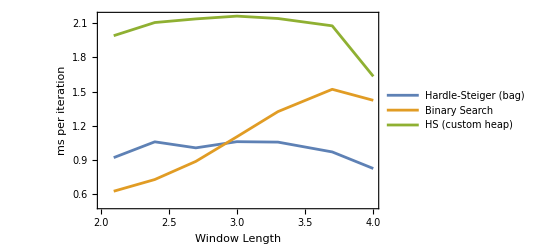

```mathematica
ListLinePlot[{tenKWinHS,tenKWinBS,tenKWinCH},ScalingFunctions->{"Log10","Log10"},
PlotLegends->{"Hardle-Steiger (bag) ","Binary Search","HS (custom heap)"},Frame->True,FrameLabel->{{"ms per iteration",""},{"Window Length","Running Windowed Median, Data=10,000"}}]
```

Less effect of declining evictions. Probably some residual non-logarithmic overhead in the custom heap implementation. Custom Heap never wins. Binary Search wins for windows less that about 500 elements due to lower overhead.

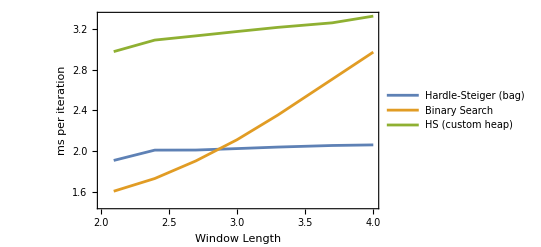

```mathematica
ListLinePlot[{hunKWinHS,hunKWinBS,hunKWinCH},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"Hardle-Steiger (bag) ","Binary Search","HS (custom heap)"},Frame->True,FrameLabel->{{"ms per iteration",""},{"Window Length","Running Windowed Median, Data=100,000"}}]
```